```mathematica
Clear[xa,ya,za,xb,yb,zb];Results=Solve[{(xb-xa)^2+(yb-ya)^2+(zb-za)^2==r1^2,Ma*xa+Mb*xb==0,Ma*ya+Mb*yb==0,Ma*za+Mb*zb==0,xa==0,ya==0},{xa,ya,za,xb,yb,zb}];
Results[[1]]
{xa,ya,za,xb,yb,zb}=Results[[1]]/.Rule[_,v_]:>v;
```

{xa→0,ya→0,za→-(Mb r1)/(√(Ma^2+2 Ma Mb+Mb^2)),xb→0,yb→0,zb→(Ma r1)/(√((Ma+Mb)^2))}

```mathematica
Clear[Ma,Mb,Mc,xa,ya,za,xb,yb,zb,xc,yc,zc,r1,r2,r3];Results=Solve[{(xb-xa)^2+(yb-ya)^2+(zb-za)^2==r1^2,(xc-xa)^2+(yc-ya)^2+(zc-za)^2==r2^2,(xb-xc)^2+(yb-yc)^2+(zb-zc)^2==r3^2,Ma*xa+Mb*xb+Mc*xc==0,Ma*ya+Mb*yb+Mc*yc==0,Ma*za+Mb*zb+Mc*zc==0,ya==0,za==0,zb==0},{xa,ya,za,xb,yb,zb,xc,yc,zc}];
{xa,ya,za,xb,yb,zb,xc,yc,zc}=Results[[1]]/.Rule[_,v_]:>v;
```

```mathematica
Simplify[xb]
```

(Ma (2 Mb r1^2+Mc (r1^2+r2^2-r3^2))+Mc (Mc (r1^2-r2^2-r3^2)+Mb (r1^2-r2^2+r3^2)))/(2 √((Ma+Mb+Mc)^2) √(Mb^2 r1^2+Mc^2 r2^2+Mb Mc (r1^2+r2^2-r3^2)))

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[Ma,Mb,Mc,Md,r1,r2,r3,r4,r5,r6,xa,ya,za,xb,yb,zb,xc,yc,zc,xd,yd,zd];Results=Solve[{(xb-xa)^2+(yb-ya)^2+(zb-za)^2==r1^2,(xc-xa)^2+(yc-ya)^2+(zc-za)^2==r2^2,(xd-xa)^2+(yd-ya)^2+(zd-za)^2==r3^2,
(xc-xb)^2+(yc-yb)^2+(zc-zb)^2==r4^2,(xd-xb)^2+(yd-yb)^2+(zd-zb)^2==r5^2,(xd-xc)^2+(yd-yc)^2+(zd-zc)^2==r6^2,Ma*xa+Mb*xb+Mc*xc+Md*xd==0,Ma*ya+Mb*yb+Mc*yc+Md*yd==0,Ma*za+Mb*zb+Mc*zc+Md*zd==0,Ma*ya+Mb*yb==0,za==0,zb==0},{xa,ya,za,xb,yb,zb,xc,yc,zc,xd,yd,zd}];
{xa,ya,za,xb,yb,zb,xc,yc,zc,xd,yd,zd}=Results[[1]]/.Rule[_,v_]:>v;
```

```mathematica
temp1=(Ma Mb (Mc^2 (-r1^2+r2^2+r4^2)+Md^2 (-r1^2+r3^2+r5^2)+Mc Md (-2 r1^2+r2^2+r3^2+r4^2+r5^2-2 r6^2))+Ma^2 (Mc^2 r2^2+Md^2 r3^2+Mc Md (r2^2+r3^2-r6^2))+Mb^2 (Mc^2 r4^2+Md^2 r5^2+Mc Md (r4^2+r5^2-r6^2)))
temp2=-(Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))+Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (r1^4+(r2^2-r4^2) (r3^2-r5^2)-r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2)))
Mass=Sqrt[(Ma+Mb+Mc+Md)^2]
```

Ma Mb (Mc^2 (-r1^2+r2^2+r4^2)+Md^2 (-r1^2+r3^2+r5^2)+Mc Md (-2 r1^2+r2^2+r3^2+r4^2+r5^2-2 r6^2))+Ma^2 (Mc^2 r2^2+Md^2 r3^2+Mc Md (r2^2+r3^2-r6^2))+Mb^2 (Mc^2 r4^2+Md^2 r5^2+Mc Md (r4^2+r5^2-r6^2))

-Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))-Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))-2 Mc Md (r1^4+(r2^2-r4^2) (r3^2-r5^2)-r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2))

√((Ma+Mb+Mc+Md)^2)

```mathematica
Simplify[yd]*temp1*temp2
```

-1/2 ⅈ Mc (Ma (Md (r3^4+2 r3^2 r4^2-r3^2 r5^2-r2^2 (r3^2+r5^2)-r3^2 r6^2+r5^2 r6^2+r1^2 (r2^2-r3^2-r6^2))+Mc (-r2^4+r4^2 (r3^2-r6^2)+r1^2 (r2^2-r3^2+r6^2)+r2^2 (r3^2+r4^2-2 r5^2+r6^2)))+Mb (Md (r3^2 (r4^2+r5^2-r6^2)+r5^2 (-2 r2^2+r4^2-r5^2+r6^2)+r1^2 (-r4^2+r5^2+r6^2))-Mc (r2^2 (r4^2+r5^2-r6^2)+r1^2 (r4^2-r5^2+r6^2)+r4^2 (-2 r3^2-r4^2+r5^2+r6^2))))

```mathematica
Simplify[zc]
```

-((ⅈ Md √(r2^4 r5^2+r1^4 r6^2+r4^2 (r3^4+r5^2 r6^2+r3^2 (r4^2-r5^2-r6^2))+r1^2 (r2^2 (r4^2-r5^2-r6^2)+r6^2 (-r4^2-r5^2+r6^2)-r3^2 (r4^2-r5^2+r6^2))-r2^2 (r3^2 (r4^2+r5^2-r6^2)+r5^2 (r4^2-r5^2+r6^2))))/(√(-Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))-Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (-r1^4-(r2^2-r4^2) (r3^2-r5^2)+r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2)))))

```mathematica
Simplify[ya]
```

-((ⅈ Mb √(Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))+Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (r1^4+(r2^2-r4^2) (r3^2-r5^2)-r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2))))/(2 √(Ma Mb (Mc^2 (-r1^2+r2^2+r4^2)+Md^2 (-r1^2+r3^2+r5^2)+Mc Md (-2 r1^2+r2^2+r3^2+r4^2+r5^2-2 r6^2))+Ma^2 (Mc^2 r2^2+Md^2 r3^2+Mc Md (r2^2+r3^2-r6^2))+Mb^2 (Mc^2 r4^2+Md^2 r5^2+Mc Md (r4^2+r5^2-r6^2)))))

```mathematica
Simplify[zc]
```

-((ⅈ Md √(r2^4 r5^2+r1^4 r6^2+r4^2 (r3^4+r5^2 r6^2+r3^2 (r4^2-r5^2-r6^2))+r1^2 (r2^2 (r4^2-r5^2-r6^2)+r6^2 (-r4^2-r5^2+r6^2)-r3^2 (r4^2-r5^2+r6^2))-r2^2 (r3^2 (r4^2+r5^2-r6^2)+r5^2 (r4^2-r5^2+r6^2))))/(√(-Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))-Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (-r1^4-(r2^2-r4^2) (r3^2-r5^2)+r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2)))))

```mathematica
ya/yb
```

-Mb/Ma

```mathematica
Clear[r1,r2,r3,r4,r5,r6,Ma,Mb,Mc,Md];
```

```mathematica
Clear[r1,r2,r3,r4,r5,r6,Ma,Mb,Mc,Md];r1=6.9194;r2=6.5;r3=13.786;r4=9.1578;r5=7.7670;r6=7.2856;Ma=41907.786918679602;Mc=Ma;Mb=155798.26813440604;Md=Mb;
{xa,ya,za}
{xb,yb,zb}
{xc,yc,zc}
{xd,yd,zd}
Sqrt[(xa-xc)^2+(ya-yc)^2+(za-zc)^2]
```

{-7.27024,4.45818+0. ⅈ,0}

{-3.28624,-1.19919+0. ⅈ,0}

{2.06286,10.4772+0. ⅈ,0.-9.00472 ⅈ}

{4.68696,-2.81823+0. ⅈ,0.+2.42216 ⅈ}

6.5+0. ⅈ

```mathematica
r1^2+r2^2+r5^2+r6^2
r3^2+r4^2
```

203.307

273.478

```mathematica
Mb/(Ma+Mb)*12.5
Mc/(Mc+Md)*8
Sqrt[(Mb/(Ma+Mb)*12.5)^2+(Md/(Mc+Md)*8)^2]
```

9.85037

1.69576

11.695

3.51789×10^11

0.113042

```mathematica
(ⅈ Md √(r2^4 r5^2+r1^4 r6^2+r4^2 (r3^4+r5^2 r6^2+r3^2 (r4^2-r5^2-r6^2))+r1^2 (r2^2 (r4^2-r5^2-r6^2)+r6^2 (-r4^2-r5^2+r6^2)-r3^2 (r4^2-r5^2+r6^2))-r2^2 (r3^2 (r4^2+r5^2-r6^2)+r5^2 (r4^2-r5^2+r6^2))))
```

0.+2.75482×10^8 ⅈ

```mathematica
(√(-Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))-Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (-r1^4-(r2^2-r4^2) (r3^2-r5^2)+r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2))))
```

0.113042

```mathematica
(Mb^2 r1^2+Mc^2 r2^2+Md^2 r3^2+Mb (Mc (r1^2+r2^2-r4^2)+Md (r1^2+r3^2-r5^2))+Mc Md (r2^2+r3^2-r6^2))
```

4.91987×10^13

```mathematica
r1=r3;r1=r4;r1=r6;
r3=r4;r3=r6;r4=r6;
Ma=Mc;
Mb=Md;
```

```mathematica
InputForm[Simplify[yc]]
```

(Sqrt[-(Mc^2*(r1^4 + (r2^2 - r4^2)^2 - 2*r1^2*(r2^2 + r4^2))) - 
    Md^2*(r1^4 + (r3^2 - r5^2)^2 - 2*r1^2*(r3^2 + r5^2)) + 
    2*Mc*Md*(-r1^4 - (r2^2 - r4^2)*(r3^2 - r5^2) + 
      r1^2*(r2^2 + r3^2 + r4^2 + r5^2 - 2*r6^2))]*
  (Mb*(Mc*(r1^4 + (r2^2 - r4^2)^2 - 2*r1^2*(r2^2 + r4^2)) + 
     Md*(r1^4 + (r2^2 - r4^2)*(r3^2 - r5^2) - 
       r1^2*(r2^2 + r3^2 + r4^2 + r5^2 - 2*r6^2))) + 
   Md*(Md*(-r3^4 - 2*r3^2*r4^2 + r3^2*r5^2 + r2^2*(r3^2 + r5^2) + 
       r3^2*r6^2 - r5^2*r6^2 + r1^2*(-r2^2 + r3^2 + r6^2)) - 
     Mc*(-r2^4 + r4^2*(r3^2 - r6^2) + r1^2*(r2^2 - r3^2 + r6^2) + 
       r2^2*(r3^2 + r4^2 - 2*r5^2 + r6^2)))))/
 (2*Sqrt[Mb^2*r1^2 + Mc^2*r2^2 + Md^2*r3^2 + 
    Mb*(Mc*(r1^2 + r2^2 - r4^2) + Md*(r1^2 + r3^2 - r5^2)) + 
    Mc*Md*(r2^2 + r3^2 - r6^2)]*
  (Mc^2*(r1^4 + (r2^2 - r4^2)^2 - 2*r1^2*(r2^2 + r4^2)) + 
   Md^2*(r1^4 + (r3^2 - r5^2)^2 - 2*r1^2*(r3^2 + r5^2)) + 
   2*Mc*Md*(r1^4 + (r2^2 - r4^2)*(r3^2 - r5^2) - 
     r1^2*(r2^2 + r3^2 + r4^2 + r5^2 - 2*r6^2))))

```mathematica
Simplify[zd]
```

(ⅈ Mc √(r2^4 r5^2+r1^4 r6^2+r4^2 (r3^4+r5^2 r6^2+r3^2 (r4^2-r5^2-r6^2))+r1^2 (r2^2 (r4^2-r5^2-r6^2)+r6^2 (-r4^2-r5^2+r6^2)-r3^2 (r4^2-r5^2+r6^2))-r2^2 (r3^2 (r4^2+r5^2-r6^2)+r5^2 (r4^2-r5^2+r6^2))))/(√(-Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))-Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (-r1^4-(r2^2-r4^2) (r3^2-r5^2)+r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2))))

```mathematica
InputForm[Simplify[zd]]
```

(I*Mc*Sqrt[r2^4*r5^2 + r1^4*r6^2 + r4^2*(r3^4 + r5^2*r6^2 + 
      r3^2*(r4^2 - r5^2 - r6^2)) + r1^2*(r2^2*(r4^2 - r5^2 - r6^2) + 
      r6^2*(-r4^2 - r5^2 + r6^2) - r3^2*(r4^2 - r5^2 + r6^2)) - 
    r2^2*(r3^2*(r4^2 + r5^2 - r6^2) + r5^2*(r4^2 - r5^2 + r6^2))])/
 Sqrt[-(Mc^2*(r1^4 + (r2^2 - r4^2)^2 - 2*r1^2*(r2^2 + r4^2))) - 
   Md^2*(r1^4 + (r3^2 - r5^2)^2 - 2*r1^2*(r3^2 + r5^2)) + 
   2*Mc*Md*(-r1^4 - (r2^2 - r4^2)*(r3^2 - r5^2) + 
     r1^2*(r2^2 + r3^2 + r4^2 + r5^2 - 2*r6^2))]

```mathematica
Clear[xa,ya,za,xb,yb,zb,xc,yc,zc,xd,yd,zd];
xa=-r12*Sin[the1]/2;
ya=0;
za=-r12*Cos[the1]/2-R/2;
xb=r12*Sin[the1]/2;
yb=0;
zb=r12*Cos[the1]/2-R/2;
xc=-r34*Sin[the2]*Cos[phi]/2;
yc=-r34*Sin[the2]*Sin[phi]/2;
zc=-r34*Cos[the2]/2+R/2;
xd=r34*Sin[the2]*Cos[phi]/2;
yd=r34*Sin[the2]*Sin[phi]/2;
zd=r34*Cos[the2]/2+R/2;
```

```mathematica
Simplify[(xc-xb)^2+(yc-yb)^2+(zc-zb)^2]
```

1/4 (4 R^2+r12^2+r34^2-4 R r12 Cos[the1]-4 R r34 Cos[the2]+2 r12 r34 Cos[the1] Cos[the2]+2 r12 r34 Cos[phi] Sin[the1] Sin[the2])

```mathematica
tot[r1_,r2_,r3_,r4_,r5_,r6_]:=(Mc^2*(r1^4+(r2^2-r4^2)^2-2*r1^2*(r2^2+r4^2))+ Md^2*(r1^4+(r3^2 - r5^2)^2 - 2*r1^2*(r3^2 + r5^2))+Mc*Md*(r1^4 + (r2^2 - r4^2)*(r3^2 - r5^2) -r1^2*(r2^2 + r3^2 + r4^2 + r5^2 - 2*r6^2)))
```

```mathematica
Mc=1;Md=2;FindMinimum[{Abs[tot[r1,r2,r3,r4,r5,r6]]},{{r1,5},{r2,5},{r3,5},{r4,5},{r5,5},{r6,6}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.40647×10^-19,{r1→1.24155×10^-11,r2→3.90364,r3→1.67811,r4→3.90364,r5→1.67811,r6→6.98599}}

```mathematica
Clear[d1,d2,d3,d4,d5,d6,r,r1,r2,t1,t2,t3];Results=Solve[{d1==r1,d2==Sqrt[4*r^2+r1^2+r2^2+4*r*r1*Cos[t1]-4*r*r2*Cos[t2]-2*r1*r2*Cos[t1]*Cos[t2]-2*r1*r2*Sin[t1]*Sin[t2]*Cos[t3]]/2,d3==Sqrt[4*r^2+r1^2+r2^2+4*r*r1*Cos[t1]+4*r*r2*Cos[t2]+2*r1*r2*Cos[t1]*Cos[t2]+2*r1*r2*Sin[t1]*Sin[t2]*Cos[t3]]/2,d4==Sqrt[4*r^2+r1^2+r2^2-4*r*r1*Cos[t1]-4*r*r2*Cos[t2]+2*r1*r2*Cos[t1]*Cos[t2]+2*r1*r2*Sin[t1]*Sin[t2]*Cos[t3]]/2,d5==Sqrt[4*r^2+r1^2+r2^2-4*r*r1*Cos[t1]+4*r*r2*Cos[t2]-2*r1*r2*Cos[t1]*Cos[t2]-2*r1*r2*Sin[t1]*Sin[t2]*Cos[t3]]/2,d6==r2},{r,r1,r2,t1,t2,t3}];
Results[[1]]
{r,r1,r2,t1,t2,t3}=Results[[1]]/.Rule[_,v_]:>v;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→(-(ⅈ d1^2 d2^4 d6)/(2 (1) √(d1^2-d2^2-d3^2-d4^2-d5^2+d6^2))+(ⅈ 2 d6)/1+54)/(-2 d3^2+2 d4^2),r1→d1,1,1,t2→-ArcCos[-1],t3→-ArcCos[(-(4 4 √1)/(√(9+d6^2))+64)/(4 d1^4 d2^4-4 d1^2 d2^6+136+4 d5^4 d6^4+16 d1^2 d6^6)]}
 |  |  |  |

```mathematica
InputForm[Simplify[t2]]
```

-ArcCos[((-I/2)*(d2^2 - d3^2 + d4^2 - d5^2))/
   (d6*Sqrt[d1^2 - d2^2 - d3^2 - d4^2 - d5^2 + d6^2])]

```mathematica
InputForm[Simplify[r]]
```

(-I/2)*Sqrt[d1^2 - d2^2 - d3^2 - d4^2 - d5^2 + d6^2]

```mathematica
InputForm[Simplify[t3]]
```

-ArcCos[(d6*Sqrt[4*d1^4 + (d2^2 + d3^2 - d4^2 - d5^2)^2 - 
      4*d1^2*(d2^2 + d3^2 + d4^2 + d5^2 - d6^2)]*
    Sqrt[-((d2^4 + d3^4 + d4^4 - 2*d4^2*d5^2 + d5^4 + 4*d1^2*d6^2 - 
        4*d4^2*d6^2 - 4*d5^2*d6^2 + 4*d6^4 - 
        2*d3^2*(d4^2 - d5^2 + 2*d6^2) - 2*d2^2*(d3^2 - d4^2 + d5^2 + 
          2*d6^2))/(d6^2*(-d1^2 + d2^2 + d3^2 + d4^2 + d5^2 - d6^2)))]*
    (-d2^6 + d3^6 + 7*d3^4*d4^2 + 7*d3^2*d4^4 + d4^6 + d3^4*d5^2 + 
     6*d3^2*d4^2*d5^2 + d4^4*d5^2 - d3^2*d5^4 - d4^2*d5^4 - d5^6 - 
     2*d1^4*(d2^2 - d3^2 - d4^2 + d5^2) - 3*d3^4*d6^2 - 10*d3^2*d4^2*d6^2 - 
     3*d4^4*d6^2 + 3*d5^4*d6^2 + 2*d3^2*d6^4 + 2*d4^2*d6^4 - 2*d5^2*d6^4 - 
     d2^4*(d3^2 + d4^2 + 7*d5^2 - 3*d6^2) + 
     d2^2*(d3^4 + d4^4 - 6*d4^2*d5^2 - 7*d5^4 + 6*d3^2*(d4^2 - d5^2) + 
       10*d5^2*d6^2 - 2*d6^4) + d1^2*(3*d2^4 - 3*d3^4 - 3*d4^4 + 3*d5^4 + 
       4*d4^2*d6^2 - 4*d5^2*d6^2 + 2*d2^2*(5*d5^2 - 2*d6^2) + 
       d3^2*(-10*d4^2 + 4*d6^2))))/
   (Sqrt[d1^2 - d2^2 - d3^2 - d4^2 - d5^2 + d6^2]*
    (16*d1^6*d6^2 + (d2^2 + d3^2 - d4^2 - d5^2)^2*(d2^4 + d3^4 + d4^4 - 
       2*d4^2*d5^2 + d5^4 - 4*d4^2*d6^2 - 4*d5^2*d6^2 + 4*d6^4 - 
       2*d3^2*(d4^2 - d5^2 + 2*d6^2) - 2*d2^2*(d3^2 - d4^2 + d5^2 + 
         2*d6^2)) + 4*d1^4*(d2^4 + d3^4 + d4^4 - 2*d4^2*d5^2 + d5^4 - 
       8*d4^2*d6^2 - 8*d5^2*d6^2 + 8*d6^4 - 2*d3^2*(d4^2 - d5^2 + 4*d6^2) - 
       2*d2^2*(d3^2 - d4^2 + d5^2 + 4*d6^2)) - 
     4*d1^2*(d2^6 + d3^6 + d4^6 - d4^4*d5^2 - d4^2*d5^4 + d5^6 - 
       6*d4^4*d6^2 - 8*d4^2*d5^2*d6^2 - 6*d5^4*d6^2 + 8*d4^2*d6^4 + 
       8*d5^2*d6^4 - 4*d6^6 - d3^4*(d4^2 - 3*d5^2 + 6*d6^2) - 
       d2^4*(d3^2 - 3*d4^2 + d5^2 + 6*d6^2) - 
       d3^2*(d4^4 - 3*d5^4 + 8*d5^2*d6^2 - 8*d6^4 + 
         2*d4^2*(d5^2 + 2*d6^2)) - d2^2*(d3^4 - 3*d4^4 + d5^4 + 
         4*d5^2*d6^2 - 8*d6^4 + 2*d4^2*(d5^2 + 4*d6^2) + 
         2*d3^2*(d4^2 + d5^2 + 4*d6^2)))))]

```mathematica
7.295800000000 9.085897838574 7.387267263064 7.879473493753 9.030269906946 15.070800000000
```

```mathematica
0.316000000000 7.295800000000 15.070800000000 134.875000000000 116.575000000000 146.975000000000
```

```mathematica
-ArcCos[((1/2)*(9.085897838574^2 +7.387267263064^2 - 7.879473493753^2 - 9.030269906946^2))/
(7.2958*Sqrt[-7.2958^2 + 9.085897838574^2 + 7.387267263064^2 + 7.879473493753^2 + 9.030269906946^2 - 15.07080^2])]*180/Pi
```

-134.875

```mathematica
-ArcCos[((1/2)*(7.295800000000^2 +7.387267263064^2 - 7.879473493753^2 - 15.070800^2))/
(9.085897838574*Sqrt[7.2958^2 - 9.085897838574^2 + 7.387267263064^2 + 7.879473493753^2 - 9.030269906946^2 + 15.07080^2])]*180/Pi
```

-130.855

```mathematica
(7.295800000000^2 +7.387267263064^2 - 7.879473493753^2 - 15.070800^2)
```

-181.415

```mathematica
7.2958*Sqrt[7.2958^2 - 9.085897838574^2 + 7.387267263064^2 + 7.879473493753^2 - 9.030269906946^2 + 15.07080^2]
```

111.346

```mathematica
ArcCos[3]
```

```mathematica
ArcCos[1.5]
```

0.+0.962424 ⅈ

```mathematica
((-1/2)*(7.295800000000^2 +7.387267263064^2 - 7.879473493753^2 - 15.070800^2))/
(7.2958*Sqrt[7.2958^2 - 9.085897838574^2 + 7.387267263064^2 + 7.879473493753^2 - 9.030269906946^2 + 15.07080^2])
```

0.814647

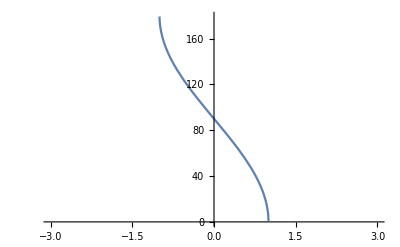

```mathematica
Plot[ArcCos[x]*180/Pi,{x,-3,3}]
```

```mathematica
-130-90+180
```

-40

```mathematica
Clear[Ma,Mb,Mc,Md,r1,r2,r3,r4,r5,r6,xa,ya,za,xb,yb,zb,xc,yc,zc,xd,yd,zd];Results=Solve[{(xb-xa)^2==1/(Mc+Md)^2(Md^2 r3^2+Mc^2 (r2^2+r4^2)+Md^2 r5^2+Mc Md (r2^2+r3^2+r4^2+r5^2-2 r6^2)-2 √((Mc^2 r2^2+Md^2 r3^2+Mc Md (r2^2+r3^2-r6^2)) (Mc^2 r4^2+Md^2 r5^2+Mc Md (r4^2+r5^2-r6^2)))),(xc-xa)^2+(yc)^2+(zc)^2==r2^2,(xd-xa)^2+(yd)^2+(zd)^2==r3^2,
(xc-xb)^2+(yc)^2+(zc)^2==r4^2,(xd-xb)^2+(yd)^2+(zd)^2==r5^2,(xd-xc)^2+(yd-yc)^2+(zd-zc)^2==r6^2,Ma*xa+Mb*xb+Mc*xc+Md*xd==0,Mc*yc+Md*yd==0,Mc*zc+Md*zd==0},{xa,xb,xc,yc,zc,xd,yd,zd}];
Results[[1]]
{xa,xb,xc,yc,zc,xd,yd,zd}=Results[[1]]/.Rule[_,v_]:>v;
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Part::partw: Part 1 of {} does not exist.

Set::shape: Lists {xa,xb,xc,yc,zc,xd,yd,zd} and {}⟦1⟧ are not the same shape.

```mathematica
Res=Solve[{√-(Mc^2 (r1^4+(r2^2-r4^2)^2-2 r1^2 (r2^2+r4^2))+Md^2 (r1^4+(r3^2-r5^2)^2-2 r1^2 (r3^2+r5^2))+2 Mc Md (r1^4+(r2^2-r4^2) (r3^2-r5^2)-r1^2 (r2^2+r3^2+r4^2+r5^2-2 r6^2)))==0},{r1}];
{rr1}=Res[[1]]/.Rule[_,v_]:>v;
```

```mathematica
Simplify[rr1^2]
```

1/(Mc+Md)^2(Md^2 r3^2+Mc^2 (r2^2+r4^2)+Md^2 r5^2+Mc Md (r2^2+r3^2+r4^2+r5^2-2 r6^2)-2 √((Mc^2 r2^2+Md^2 r3^2+Mc Md (r2^2+r3^2-r6^2)) (Mc^2 r4^2+Md^2 r5^2+Mc Md (r4^2+r5^2-r6^2))))

```mathematica
Simplify[(xb-xa)*(xd-xc)+(yb-ya)*(yd-yc)+(zb-za)*(zd-zc)]
```

1/2 (-r2^2+r3^2+r4^2-r5^2)

```mathematica
Simplify[(xb-xa)*(xd-xc)+(yb-ya)*(yd-yc)]
```

1/2 (-r2^2+r3^2+r4^2-r5^2)